ω0 = 274.783 rad/s

G = 65.3333

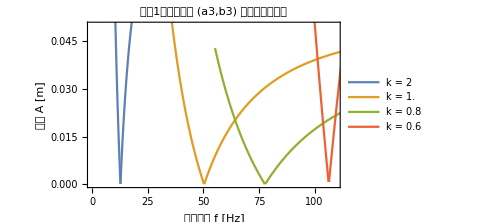

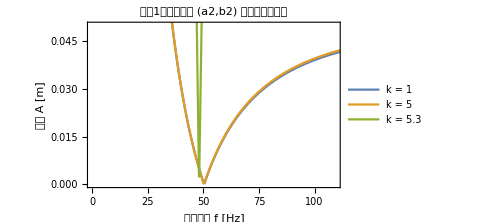

数据已导出到 D:\unstable_regions1111.xlsx

```mathematica
(*清除所有变量*)ClearAll["Global`*"];

(* ==================物理参数（固定）==================*)
l1=0.15;(*杆1长度[m]*)d1=0.006;(*杆1直径[m]*)EE=15.069*10^9;(*弹性模量[Pa]*)ρ=887;(*密度[kg/m^3]*)g=9.8;(*重力加速度[m/s^2]*)ω0=Sqrt[EE*d1^2/(16*ρ*l1^4)];(*参考频率[rad/s]*)G=g/l1;(*无量纲重力项*)Print["ω0 = ",ω0," rad/s"];
Print["G = ",G];

(*阻尼系数（固定）*)
d1d=0;d2d=0;d3d=0;
damping=DiagonalMatrix[{d1d,d2d,d3d}];

(* ==================基准比例参数==================*)
a2base=0.333;b2base=0.333;a3base=0.137;b3base=1.04;

(* ==================定义计算模态1边界的函数（修正版）==================*)
GetMode1Boundary[{a2_,b2_,a3_,b3_},εlist_]:=Module[{A11,A12,A13,A22,A33,B1,M,K0,K1,vals,vecs,minIndex,ω1,vec1,Uall,overlaps,idx1,Ucol,u1,Cmodal,ζ1,γ1,εvalid,r,validIdx,Ωminus,Ωplus,A},(*计算常数系数*)A11=1/3+a2 (1-b2+b2^2/3)+a3 (1+b3^2/3);
A12=a2 (b2^2/3-b2/2);
A13=a3 b3^2/3;
A22=a2 b2^2/3;
A33=a3 b3^2/3;
B1=1/2+a2+a3+(a2 b2)/2;
M={{A11,A12,A13},{A12,A22,0},{A13,0,A33}};
K0={{ω0^2-B1 G,-(a2 b2)/2 G,0},{-(a2 b2)/2 G,(a2^2/b2^3) ω0^2-(a2 b2)/2 G,0},{0,0,(a3^2/b3^3) ω0^2}};
K1=(a3 b3)/2*{{1,0,1},{0,0,0},{1,0,1}};
(*模态分析*){vals,vecs}=Eigensystem[{K0,M}];
minIndex=Ordering[vals,1][[1]];(*最小特征值索引*)ω1=Sqrt[vals[[minIndex]]];(*模态1固有频率[rad/s]*)vec1=vecs[[minIndex]];(*模态1原始特征向量（行向量）*)(*正交归一化所有模态*)Uall=Orthogonalize[vecs,Dot[#1,M.#2]&];(*正交归一化后的行向量列表*)(*通过最大投影找到与 vec1 最匹配的模态（避免顺序错乱）*)overlaps=Table[Abs[Uall[[i]].M.vec1],{i,3}];
idx1=Position[overlaps,Max[overlaps]][[1,1]];
Ucol=Transpose[Uall];(*列向量矩阵，第 i 列对应第 i 个正交模态*)u1=Ucol[[All,idx1]];(*模态1的列向量*)(*计算模态阻尼比*)Cmodal=Transpose[Ucol].damping.Ucol;
ζ1=Cmodal[[idx1,idx1]]/(2 ω1);
(*计算耦合系数 γ1=u1^T K1 u1*)γ1=u1.K1.u1;
(*过滤 εlist，只保留大于阻尼比的值（实际阻尼为零，但保留通用性）*)εvalid=Select[εlist,#>ζ1&];
If[Length[εvalid]==0,Return[{}]];
r=Sqrt[εvalid^2-ζ1^2];
(*仅保留使 1-2r>0 的点（保证 Ωplus 为正实数）*)validIdx=Flatten[Position[r,_?(#<0.5&)]];
If[Length[validIdx]==0,Return[{}]];
εvalid=εvalid[[validIdx]];
r=r[[validIdx]];
(*计算边界：Ω=2 ω1/Sqrt[1±2 r][rad/s]*)Ωminus=2 ω1/Sqrt[1+2 r];
Ωplus=2 ω1/Sqrt[1-2 r];
(*实际振幅 A=εvalid*l1/Abs[γ1][m]*)A=εvalid*l1/Abs[γ1];
{Transpose[{Ωminus,A}],Transpose[{Ωplus,A}]}]

(* ==================绘图参数==================*)
Amax=0.05;(*振幅上限[m]*)Ωrange={0,2.5 ω0};(*角频率范围[rad/s]*)εlist=Table[ε,{ε,0.001,0.5,0.01}];(*Mathieu 小参数列表*)(*将角频率[rad/s] 转换为频率[Hz] 的函数*)toHz=(#/(2 π))&;

(* ==================定义数据块生成函数==================*)
MakeBlock[val_,curves_]:=Module[{block},If[curves=={},Return[{}]];
block={};
AppendTo[block,{ToString[val],""}];(*参数值行*)AppendTo[block,{"Left boundary",""}];
AppendTo[block,{"f- [Hz]","A [m]"}];
block=Join[block,curves[[1]]];(*左边界数据（频率已转换为 Hz）*)AppendTo[block,{"",""}];(*空行*)AppendTo[block,{"Right boundary",""}];
AppendTo[block,{"f+ [Hz]","A [m]"}];
block=Join[block,curves[[2]]];(*右边界数据*)AppendTo[block,{"",""}];
AppendTo[block,{"",""}];(*两个空行分隔*)block]

(* ==================1. a3 和 b3 按比例同时变化==================*)
klistA3B3={2,1.,0.8,0.6};(*缩放因子列表*)colors=ColorData[97]/@Range[Length[klistA3B3]];
dataA3B3={};
plotA3B3=Show[Table[Module[{curves,a3,b3},a3=klistA3B3[[i]]*a3base;
b3=klistA3B3[[i]]*b3base;
curves=GetMode1Boundary[{a2base,b2base,a3,b3},εlist];
If[curves=!={},(*将角频率转换为频率[Hz]*)curves=curves/.{x_?NumericQ,y_?NumericQ}:>{toHz[x],y};
AppendTo[dataA3B3,MakeBlock[klistA3B3[[i]],curves]];
ListLinePlot[curves,PlotStyle->{colors[[i]],colors[[i]]},Filling->{1->{2}},FillingStyle->Directive[Opacity[0.3],colors[[i]]],PlotLegends->{StringForm["k = ``",klistA3B3[[i]]]}],Nothing]],{i,Length[klistA3B3]}],PlotRange->{toHz/@Ωrange,{0,Amax}},Frame->True,FrameLabel->{"激励频率 f [Hz]","振幅 A [m]"},PlotLabel->"模态1不稳定区域 (a3,b3) 按比例同时变化",ImageSize->Medium]
If[dataA3B3=={},dataA3B3={{{"No data for a3b3 variation",""}}}];

(* ==================2. a2 和 b2 按比例同时变化==================*)
klistA2B2={1,5,5.3};(*缩放因子列表*)colors=ColorData[97]/@Range[Length[klistA2B2]];
dataA2B2={};
plotA2B2=Show[Table[Module[{curves,a2,b2},a2=klistA2B2[[i]]*a2base;
b2=klistA2B2[[i]]*b2base;
curves=GetMode1Boundary[{a2,b2,a3base,b3base},εlist];
If[curves=!={},curves=curves/.{x_?NumericQ,y_?NumericQ}:>{toHz[x],y};
AppendTo[dataA2B2,MakeBlock[klistA2B2[[i]],curves]];
ListLinePlot[curves,PlotStyle->{colors[[i]],colors[[i]]},Filling->{1->{2}},FillingStyle->Directive[Opacity[0.3],colors[[i]]],PlotLegends->{StringForm["k = ``",klistA2B2[[i]]]}],Nothing]],{i,Length[klistA2B2]}],PlotRange->{toHz/@Ωrange,{0,Amax}},Frame->True,FrameLabel->{"激励频率 f [Hz]","振幅 A [m]"},PlotLabel->"模态1不稳定区域 (a2,b2) 按比例同时变化",ImageSize->Medium]
If[dataA2B2=={},dataA2B2={{{"No data for a2b2 variation",""}}}];

(* ==================定义横向合并函数==================*)
mergeBlocks[blocks_List]:=Module[{maxLen,paddedBlocks,merged},(*如果块列表包含无数据占位符，则直接返回原样*)If[blocks=={{{"No data for a3b3 variation",""}}}||blocks=={{{"No data for a2b2 variation",""}}},Return[blocks]];
maxLen=Max[Length/@blocks];(*所有块的最大行数*)paddedBlocks=PadRight[#,maxLen,{None,None}]&/@blocks;
(*将每个块的第 i 行并排排列*)merged=Table[Flatten[Table[paddedBlocks[[j,i]],{j,Length[blocks]}]],{i,maxLen}];
merged]

(* ==================准备导出数据==================*)
exportData={"a3b3"->mergeBlocks[dataA3B3],"a2b2"->mergeBlocks[dataA2B2]};

(* ==================导出数据到 Excel==================*)
Export["D:\\unstable_regions1111.xlsx",exportData];
Print["数据已导出到 D:\\unstable_regions1111.xlsx"];
```